# Hawk-Dove Game

## Stability analysis

Reminder: Discrete strategies Hawk (H) and Dove (D)

```mathematica
wh[p_]:=Subscript[w, o]+p (v-c)/2+(1-p) v;
```

```mathematica
wd[p_]:=Subscript[w, o]+(1-p) v/2;
```

```mathematica
wb[p_]:=p wh[p]+(1-p)wd[p]
```

```mathematica
f[p_]:=(p wh[p])/wb[p]//FullSimplify
```

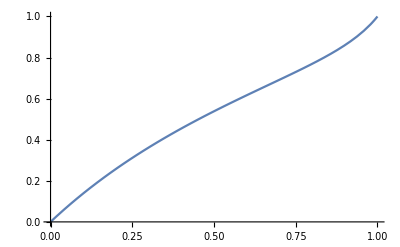

```mathematica
Plot[f[p]//.{Subscript[w, o]->1,v->2,c->3},{p,0,1}] (* plot p' as a function of p *)
```

```mathematica
equi=D[f[p],p]/.{p->v/c}//FullSimplify
```

(2 c w_o)/((c-v) v+2 c w_o)

According to McElreath & Boyd (p.45), the equilibrium p = v/c is stable whenever v < c, i.e. whenever the equilibrium exists. Here I find:

```mathematica
Refine[Reduce[equi>-1&&equi<1],{Subscript[w, o]>0,v>0,c>0}]//FullSimplify
```

(c<v&&c ((c-v) v+4 c w_o)<0)||(c>v&&c ((c-v) v+4 c w_o)>0)

Continuous stable strategies (CSS) analysis

## Fixed population size (Wright-Fisher Model)

### Analytical solution

Let us consider a family of strategies which plays hawks with probability z and dove with probability (1 - z). Let us call the dominant strategy in the population for a given value z, r (for resident); and m for a rare mutant strategy of value z + δ. Since we have a panmictic population, and strategy b is extremely rare, we assume that when any individual i encounters an individual j, j will display strategy a with probability ~1. Therefore we can write the payoff of resident and mutant strategies respectively as:

```mathematica
payoff[zi_,zj_]:=zi (zj (v-c)/2+(1-zj)v)+(1-zi)(1-zj)v/2 (* payoff for individual i with strategy zi against individual j with strategy zj *)
```

Considering p as the frequency of individuals with resident strategy in the population, we can derive the fitness of both strategies and the recursive function of p:

```mathematica
wr[p_,z_,δ_]:=Subscript[w, o]+p*payoff[z,z]+(1-p)* payoff[z,(z+δ)]
```

```mathematica
wm[p_,z_,δ_]:=Subscript[w, o]+p*payoff[(z+δ),z]+(1-p)* payoff[(z+δ),(z+δ)]
```

```mathematica
pPrime[p_,z_,δ_]:=(p wr[p,z,δ])/(p wr[p,z,δ]+(1-p) wm[p,z,δ])
```

```mathematica
Δp[p_,z_,δ_]:=pPrime[p,z,δ]-p
```

```mathematica
equi=Solve[Δp[p,z,δ]==0,p]//FullSimplify
```

{{p→0},{p→1},{p→(-v+c (z+δ))/(c δ)}}

```mathematica
(wr[p,z,δ]-wm[p,z,δ])/.{Sequence @@ Last[equi]}//FullSimplify
```

0

```mathematica
Series[(-v+c (z+δ))/(c δ),{δ,0,1}]
```

(-v/c+z)/δ+1+O[δ]^2

```mathematica
(-v+c(z+δ))/(c δ)//.{c->2,v->1,δ->0.1,z->0.99}
```

5.9

There are three equilibria to this system: 
(1) p̂→ 0, population composed of individuals with strategy family z+δ only;
(2) p̂→ 1, population composed of individuals with strategy family z only;
(3) p̂→(-v+c (z+δ))/(c δ), population with both probabilities of playing hawk (z and z+δ). NB: This equilibrium isn't biologically realistic (probability values p not within [0-1]).
What are the stability conditions for these equilibria? 
First, let us ask the question of whether a mutant with strategy z+δ can invade any population of z's when rare:

```mathematica
Refine[Reduce[(wm[p,z,δ]/.p->1)>(wr[p,z,δ]/.p->1),z],{v>0,c>0,0≤ z≤ 1}]
```

w_o∈ℝ&&((δ<0&&z>v/c)||(δ>0&&z<v/c))

A rare mutant can invade a population with strategy z, for almost any value of z between 0 and 1. The only resident strategy that cannot be invaded is z* = v/c. In other words, if the probability for an individual to play hawk equals the benefit to cost ratio of engaging into fights, the strategy cannot be invaded. However, it pays to play hawk slightly more often (δ>0) against individuals playing hawk at a lower frequency than the overall gain of a fight (z<v/c). Inversely, if the population plays hawk more often than the relative gain (z>v/c) obtained over fights, it pays to play dove and retreat slightly more often (δ<0) and thus avoid the fighting cost of say, getting injured.

Can the polymorphic population at equilibrium (equilibrium 3) be invaded by a new mutant with a probability to play hawk equal to z+ε, where ε ≠ δ ? Let us define payoff and fitness for each strategy family, considering the proportion of the original resident and the new mutant strategies to be p and q respectively. NB: This part is irrelevant, considering the polymorphic equilibrium isn't biologically realistic, but is nonetheless carried-out for practice purposes.

```mathematica
wrr[p_,q_,z_,δ_,ε_]:=Subscript[w, o]+p*payoff[z,z]+(1-p-q)* payoff[z,(z+δ)]+q*payoff[z,(z+ε)]
```

```mathematica
wrm[p_,q_,z_,δ_,ε_]:=Subscript[w, o]+p*payoff[(z+δ),z]+(1-p-q)* payoff[(z+δ),(z+δ)]+q*payoff[(z+δ),(z+ε)]
```

```mathematica
wmm[p_,q_,z_,δ_,ε_]:=Subscript[w, o]+p*payoff[(z+ε),z]+(1-p-q)* payoff[(z+ε),(z+δ)]+q*payoff[(z+ε),(z+ε)]
```

When we are at the polymorphic equilibrium, i.e  p→(polymorphic equilibrium) and p+q→1, can a rare mutant invade the population?

```mathematica
(wrr[p,q,z,δ,ε]-wrm[p,q,z,δ,ε])//.{Sequence @@ Last[equi],q->0}//FullSimplify
```

0

```mathematica
Refine[Reduce[(wmm[p,q,z,δ,ε]//.{Sequence @@ Last[equi],q->0})>(wrr[p,q,z,δ,ε]//.{Sequence @@ Last[equi],q->0}),z, Reals],{v>0,c>0,0≤ z≤ 1,0≤ δ≤ 1,0≤ ε≤ 1,Subscript[w, o]>0}]
```

False

A new mutant can never invade the population when at equilibrium p→(-v+c (z+δ))/(c δ).

### Simulations

Let us start with initial values of z = 0.1

```mathematica
init[n_]:=Table[0.1,{i,n}]
```

```mathematica
mut[z_,μ_,λ_]:=Module[{newz},
newz=z+RandomInteger[BernoulliDistribution[μ]] RandomReal[NormalDistribution[0,λ]];
Return[If[newz>1,1-10^-6,If[newz<0,10^-6,newz]]]
]
```

The fitness of an individual i with strategy z_i is determined by the payoff resulting from a game with an opponent j with strategy z_j. That is, W_i=z_i(z_j(v-c)/2+(1-z_j) v)+(1-z_i)(1-z_j)v/2. z_jis thus the probability of i's opponent to play hawk. The average probability for i's opponent to play hawk, considering equal likelihood for i to encounter any other individual in the population, is the average z in the population, individual i excluded: OverBar[z_j]=(∑_(j=1)^(n-1) z_j)/(n-1)=((∑_(k=1)^n z_k)-z_i)/(n-1). Here we make an approximation when calculating the individual fitness, by using OverBar[z_j] to estimate payoffs. Another and more accurate approach would be to use an n*n matrix, but it would be less efficient in terms of computer calculation and processing, especially with large population sizes.

```mathematica
payoff[zi_,zcorr_,n_]:=10+zi ((zcorr-zi/(n-1)) (v-c)/2+(1-zcorr+zi/(n-1)) v)+(1-zi)(1-zcorr+zi/(n-1)) v/2 (* add 10 to ensure positive payoffs *)
```

```mathematica
nextGen[zpop_,μ_,λ_,gain_,cost_,n_]:=Block[{mutpop,zcorr,gamepayoffs,repro},
mutpop=Map[mut[#,μ,λ]&,zpop];
zcorr=Total[zpop]/(n-1);
gamepayoffs=Map[payoff[#,zcorr,n]&,zpop]//.{v->gain,c->cost};
repro=RandomChoice[gamepayoffs->mutpop,n];
Return[repro]
]
```

```mathematica
genDat[n_,g_,μ_,λ_,gain_,cost_]:=Block[{zinit},
zinit=init[n];
Return[NestList[nextGen[#,μ,λ,gain,cost,n]&,zinit,g]]
]
```

```mathematica
datOut = genDat[2000,1000,0.001,0.05,3,2];
```

```mathematica
(*datOut2=genDat[2000,1000,0.001,0.05,2,3];*)
```

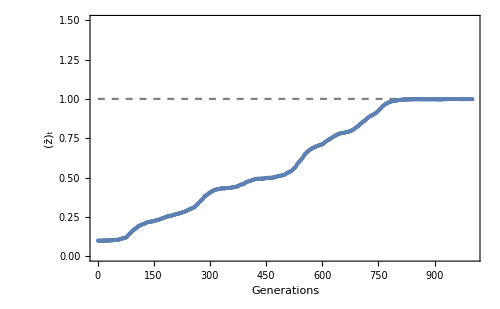

```mathematica
Show[ListPlot[Table[Mean[datOut_⟦i⟧],{i,1,Length[datOut]}],AxesOrigin->{0,0},PlotRange->{{0,Length[datOut]},{0,1.5}},FrameLabel->{Style["Generations",30],Style["(z̄)_t",30]},ImageSize->{500,Automatic},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->20],Frame->{True,True,False,False},PlotStyle->Thick],Plot[1,{x,3/2,Length[datOut]}, PlotStyle->{Gray,Dashed}]]
```

The population reaches an asymptote for z, which should be z*=v/c=3/2=1.5, but is not reachable here since 0<=z=1. When the cost of playing hawk is less than the gain of winning a fight, the probability of playing hawk at equilibrium is 1. What is the distribution of z values ?

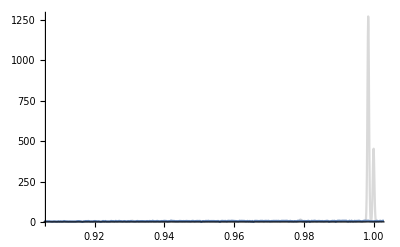

```mathematica
Show[SmoothHistogram[Last[datOut],Automatic,"PDF",PlotStyle->LightGray,PlotRange->All],Plot[PDF[FindDistribution[Last[datOut]],x],{x,0.5,1.5}]]
```

```mathematica
ℋ=DistributionFitTest[Last[datOut],Automatic,"HypothesisTestData"];
```

```mathematica
(* ℋ["TestDataTable",All] *)
```

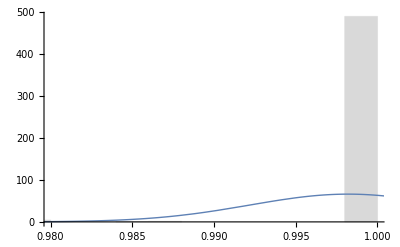

```mathematica
Show[Histogram[Last[datOut],Automatic,"PDF",ChartStyle->LightGray],Plot[PDF[ℋ["FittedDistribution"],x],{x,0.9,1.5},PlotRange->All,PlotStyle->Thick]]
```

```mathematica
datOutSmallPop = genDat[20,1000000,0.001,0.05,2,3];
```

```mathematica
Show[ListPlot[Table[Mean[datOutSmallPop_⟦i⟧],{i,1,Length[datOutSmallPop]}],AxesOrigin->{0,0},PlotRange->{{0,Length[datOutSmallPop]},{0,1.5}},FrameLabel->{Style["Generations",30],Style["(z̄)_t",30]},ImageSize->{500,Automatic},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->20],Frame->{True,True,False,False},PlotStyle->Thick],Plot[2/3,{x,1,Length[datOutSmallPop]}, PlotStyle->{Gray,Dashed}]]
```

-Graphics-

When population size is small, the population hardly reaches equilibrium, even after a long generation time.. The fixation of z*  is more erratic, and mean z values actually varies greatly around the equilibrium.

```mathematica
Last[datOutSmallPop]
```

{0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999}

Data set too small and with no variation does not allow computation of PDF.

```mathematica
varV[n_,g_,μ_,λ_,vmax_,cost_:1,nparam_:10]:=Block[{vvals,simdat},
vvals=Range[1,vmax,N[(vmax-1)/(nparam-1)]];
Return[Map[genDat[n,g,μ,λ,#,cost]&,vvals]]
](* one simulation per c value, over g generations, with n individuals. Data dimensions: {nparams,g,n} *)
```

```mathematica
datTest=Table[varV[200,100,0.001,0.05,{1,5}],{i,1,2}];
```

```mathematica
Dimensions[datTest] (* nsims,nparams,ngenerations+1,popsize *)
```

{2,10,101,200}

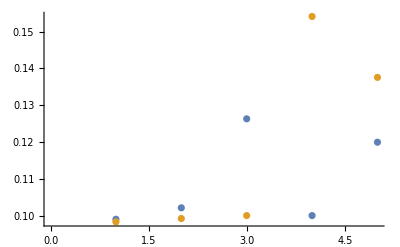

```mathematica
ListPlot[Map[Table[Mean[datTest[[#,i,-1,All]]],{i,1,5}]&,Range[2]]]
```

```mathematica
simV[nsims_,n_,g_,μ_,λ_,vmax_,cost_:1,nparam_:10]:=Block[{sims},
sims=Table[varV[n,g,μ,λ,vmax,cost,nparam],{i,1,nsims}];(* repeat simulation nsims times. Data dimensions: {nsims,nparams,g+1,n} *)
Return[ListPlot[Map[Table[Mean[sims[[#,i,-1,All]]],{i,1,nparam}]&,Range[nsims]],AxesOrigin->{0,0},PlotRange->{{0,nparam+1},{0,1.5}},FrameLabel->{Style["gain v",30],Style["(z̄)_t",30]},ImageSize->{500,Automatic},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->20],Frame->{True,True,False,False},PlotStyle->Thick]]
]
```

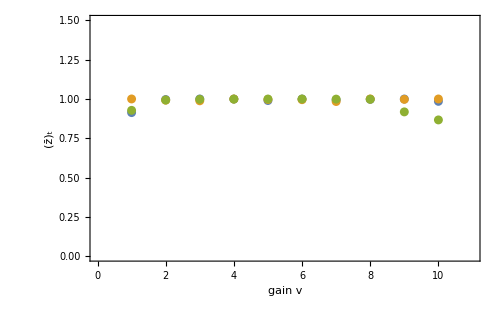
{1690.66,-Graphics-}

```mathematica
Timing[simV[3,2000,1000,0.001,0.05,5]]
```

```mathematica
varC[n_,g_,μ_,λ_,cmax_,gain_:1,nparam_:10]:=Block[{cvals,simdat},
cvals=Range[1,cmax,N[(cmax-1)/(nparam-1)]];
Return[Map[genDat[n,g,μ,λ,gain,#]&,cvals]]
](* one simulation per c value, over g generations, with n individuals. Data dimensions: {nparams,g,n} *)
```

```mathematica
simC[nsims_,n_,g_,μ_,λ_,cmax_,gain_:1,nparam_:10]:=Block[{sims},
sims=Table[varC[n,g,μ,λ,cmax,gain,nparam],{i,1,nsims}];(* repeat simulation nsims times. Data dimensions: {nsims,nparams,g,n} *)
Return[ListPlot[Map[Table[Mean[sims[[#,i,-1,All]]],{i,1,nparam}]&,Range[nsims]]]]
]
```

```mathematica
simC[3,2000,1000,0.001,0.05,1,{1,5}]
```

## Density-dependent competition (Beverton-Holt Model)

### Analytical solution

```mathematica
Clear["Global`*"]
```

We assume density-dependent competition, but density-independent selection. This means that there is competition for resources at the population level, with the strength of density-dependent competition the same for the whole population, regardless of individual strategies. Let us write n the population size, and n* the population size at equilibrium when there is no variation over generations. That is, the population reached its maximum carrying capacity size based on the available resources. We write the fitness of an individual i as w_i(N)=(f_b+π̄)/(1+γ N), where f_b is the base fecundity when there is no interaction between individual, and no competition for resources, π̄ is the mean payoff of an individual over its lifetime and depends on the other's strategies, γ measures the effect of density-dependent competition and N is the total population size. The population size at the next generation is therefore N'=w_i(N)·N. Population size at equilibrium is stable, such as ΔN=N'-N=N*·(w(N*)-1)=0 i.e. either N*=0 or w(N*)=1 ⇔ N^*=(f_b+π̄-1)/γ. The carrying capacity of the population changes over time.

### Simulations

```mathematica
Clear["Global`*"]
```

The payoffs of the game are unchanged compared to the previous simulations :

```mathematica
payoff[zi_,zcorr_,n_]:=zi ((zcorr-zi/(n-1)) (v-c)/2+(1-zcorr+zi/(n-1)) v)+(1-zi)(1-zcorr+zi/(n-1)) v/2 (* this is the mean payoff of an individual i when playing against potentially all the population *)
```

```mathematica
fitness[zi_,zcorr_,n_]:=(Subscript[f, o]+payoff[zi,zcorr,n])/(1+γ n) (* per capita number of offspring that make it to adulthood. Subscript[f, o] is the basal fecundity of an individual *)
```

Let us start with initial values of z = 0.1

```mathematica
init[n_]:=Table[0.1,{i,n}]
```

```mathematica
mut[z_,μ_,λ_]:=Module[{newz},
newz=z+RandomInteger[BernoulliDistribution[μ]] RandomReal[NormalDistribution[0,λ]];
Return[If[newz>1,1-10^-6,If[newz<0,10^-6,newz]]]
]
```

```mathematica
nextGen[zpop_,fbase_,gamma_,gain_,cost_,μ_,λ_]:=Block[{mutPop,n,zcorr,fitPop},
mutPop=Map[mut[#,μ,λ]&,zpop];
n=Length[zpop]; (* population size at time t *)
zcorr=Total[zpop]/(n-1);
fitPop=Map[fitness[#,zcorr,n]&,mutPop]//.{Subscript[f, o]-> fbase, v-> gain,c-> cost,γ->gamma};
Return[RandomChoice[fitPop->mutPop,Round[Total[fitPop]]]](* population size at the next generation is the sum of the individual fitnesses in the population, rounded in order to obtain an integer. *)
]
```

Population size is deterministic in this model: there is no ecological stochasticity, and a single ecological attractor that determines population size. Genetic stochasticity is taken into account with mutation and the introduction of genetic drift (random choice of z gametes produced weighted by individual fitness).

```mathematica
nextGen[{0.1,0.2,0.3},10,1.2,3,2,0.5,0.005]
```

{0.301938,0.0939849,0.0939849,0.198645,0.0939849,0.198645,0.198645}

```mathematica
genDat[n_,gen_,μ_,λ_,gain_,cost_,fbase_,gamma_]:=Block[{zinit,datOut,zevol,nevol},
zinit=init[n];
datOut=NestList[nextGen[#,fbase,gamma,gain,cost,μ,λ]&,zinit,gen];
zevol=Show[ListPlot[Table[Mean[datOut_[[i]]],{i,1,Length[datOut]}],AxesOrigin->{0,0},PlotRange->{{0,Length[datOut]},{0,1.2}},FrameLabel->{Style["Generations",30],Style["(z̄)_t",30]},ImageSize->{500,Automatic},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->20],Frame->{True,True,False,False},PlotStyle->Thick],Plot[gain/cost,{i,0,Length[datOut]},PlotStyle->{Gray,Dashed}]];
nevol=Show[ListPlot[Table[Length[datOut_[[i]]],{i,1,Length[datOut]}],AxesOrigin->{0,0},PlotRange->Automatic,FrameLabel->{Style["Generations",30],Style["N",30]},ImageSize->{500,Automatic},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->20],Frame->{True,True,False,False},PlotStyle->Thick],ListPlot[Table[(fbase-1)/gamma//.{v->gain,c->cost},{i,0,Length[datOut]}],PlotStyle->{Gray,Dashed}]] ;
CellPrint@ExpressionCell[#,"Output"]&/@{zevol,nevol};
]
```

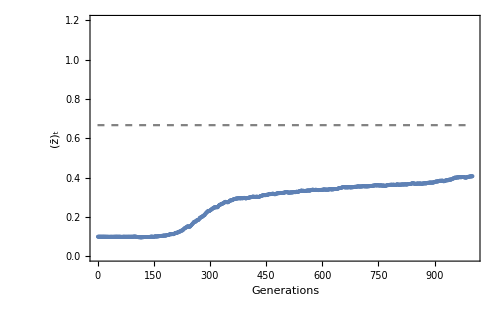

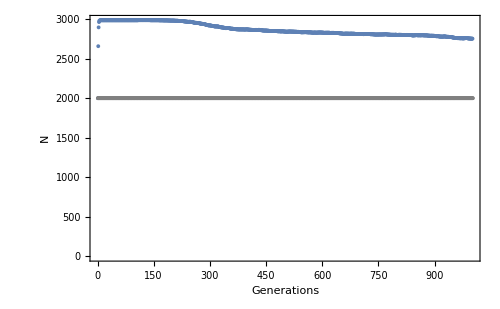

```mathematica
genDat[2000,1000,0.001,0.05,2,3,3,0.001]
```

```mathematica
varV[n_,g_,μ_,λ_,vmax_,fbase_,gamma_,cost_:1,nparam_:10]:=Block[{vvals,simdat},
vvals=Range[1,vmax,N[(vmax-1)/(nparam-1)]];
Return[Map[genDat[n,g,μ,λ,#,cost,fbase,gamma]&,vvals]]
](* one simulation per c value, over g generations, with n individuals. Data dimensions: {nparams,g,n} *)
```

```mathematica
simV[nsims_,n_,g_,μ_,λ_,vmax_,fbase_,gamma_,cost_:1,nparam_:10]:=Block[{sims},
sims=Table[varV[n,g,μ,λ,vmax,fbase,gamma,cost,nparam],{i,1,nsims}];(* repeat simulation nsims times. Data dimensions: {nsims,nparams,g,n} *)
Return[Show[Plot[x/cost,{x,1,vmax}],
ListPlot[Map[Table[Mean[sims[[#,i,-1,All]]],{i,1,vmax}]&,Range[nsims]],AxesOrigin->{0,0},PlotRange->{{0,vmax+1},{0,1.5}},FrameLabel->{Style["gain v",30],Style["(z̄)_t",30]},ImageSize->{500,Automatic},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->20],Frame->{True,True,False,False},PlotStyle->Thick]]
]
```

```mathematica
Timing[simV[3,2000,1000,0.001,0.05,{1,5},3,2]]
```

```mathematica
varC[n_,g_,μ_,λ_,crange_List,fbase_,gamma_,gain_:1,nparam_:10]:=Block[{cvals,simdat},
cvals=Range[crange[[1]],crange[[2]],N[(crange[[2]]-crange[[1]])/(nparam-1)]];
Return[Map[genDat[n,g,μ,λ,gain,#,fbase,gamma]&,cvals]]
](* one simulation per c value, over g generations, with n individuals. Data dimensions: {nparams,g,n} *)
```

```mathematica
simC[nsims_,n_,g_,μ_,λ_,crange_List,fbase_,gamma_,cost_:1,nparam_:10]:=Block[{sims},
sims=Table[varC[n,g,μ,λ,crange,fbase,gamma,cost,nparam],{i,1,nsims}];(* repeat simulation nsims times. Data dimensions: {nsims,nparams,g,n} *)
Return[ListPlot[Map[Table[Mean[sims[[#,i,-1,All]]],{i,1,nparam}]&,Range[nsims]],AxesOrigin->{0,0},PlotRange->{{0,nparam+1},{0,1.5}},FrameLabel->{Style["gain v",30],Style["(z̄)_t",30]},ImageSize->{500,Automatic},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->20],Frame->{True,True,False,False},PlotStyle->Thick]]
]
```

```mathematica
Timing[simC[3,2000,1000,0.001,0.05,{1,5},3,2]]
```

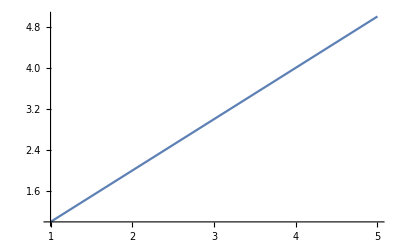

```mathematica
Plot[v,{v,1,5}]
```